```mathematica
V=Vpk Sin[2π τ+α];
Integrate[γ V,{τ,0,t/2}]-Integrate[γ V,{τ,t/2,t}]//FullSimplify
```

-(2 Cos[π t] Sin[(π t)/2]^2)/π

```mathematica
%/.t->1
```

2/π

```mathematica
(2 Vpk γ Sin[(π t)/2]^2 Sin[π t+α])/π/.t->1
```

0

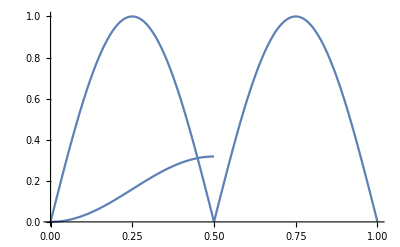

```mathematica
tmax=1;
Vpk=1;
α=0;
γ=1;
Show[Plot[V/.τ->t,{t,0,tmax/2}],Plot[-V/.τ->t,{t,tmax/2,tmax}],Plot[Integrate[V,{τ,0,t}],{t,0,tmax/2}],PlotRange->All]
```

```mathematica
Integrate[γ V,{τ,0,t/2}]/.t->1
```

0